```mathematica
Graphics3D[{{Opacity[0.1],Sphere[{5,1,1.5},1.5],White,Sphere[{5,1,4},1.1]},Black,Sphere[{4,1.3,4.3},0.13],Black,Sphere[{4,0.8,4.3},0.13],Orange,Cylinder[{{3.5,1.0,3.6},{4.1,1,4}},1/8]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[.5],Glow[Yellow],EdgeForm[Gray],PolyhedronData["SnubCube","Faces"]},Lighting->None]
```

-Graphics3D-

```mathematica
Tetrahedron[ ]
```

Tetrahedron[]

Show::gcomb: Could not combine the graphics objects in {{GraphicsBox[List[List[List[], List[], List[Hue[Skeleton[3]], LineBox[Skeleton[1]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[Skeleton[2]], List[Skeleton[2]]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]]], 0}, Graphics3DBox[List[SphereBox[List[1, 0.3`, 0.3`], 0.13`], GrayLevel[0], List[Opacity[0.5`], Glow[RGBColor[1, 1, 0]], EdgeForm[GrayLevel[0.5`]], GraphicsComplex3DBox[List[List[Skeleton[3]], List[Skeleton[3]], List[Skeleton[3]], List[Skeleton[3]], List[Skeleton[3]], List[Skeleton[3]]], Polygon3DBox[List[Skeleton[5]]]]]], Rule[Lighting, None]]}.

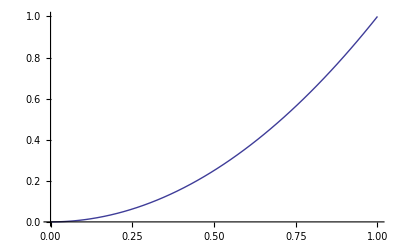
Show[{{-Graphics-,0},-Graphics3D-}]

```mathematica
g=Plot[x^2,{x,0,1}];
Show[{{g,0},Graphics3D[{Sphere[{1,0.3,0.3},0.13],Black,{Opacity[.5],Glow[Yellow],EdgeForm[Gray],PolyhedronData[{"Prism",3},"Faces"]}},Lighting->None]}]
```

```mathematica
PolyhedronData[{"Prism",3},"Image"]
```

-Graphics3D-

```mathematica
PolyhedronData[{"Prism",3}]
```

-Graphics3D-

```mathematica
PolyhedronData["Properties"]
```

PolyhedronData[Properties]

```mathematica
PolyhedronData["Properties"]
```

{AdjacentFaceIndices,AlternateNames,AlternateStandardNames,Amphichiral,Antiprism,Archimedean,ArchimedeanDual,Centroid,Chiral,Circumcenter,Circumradius,Circumsphere,Classes,Compound,Concave,Convex,Cuboid,DefaultOrientation,Deltahedron,DihedralAngleRules,DihedralAngles,Dipyramid,DualCompound,DualName,DualScale,EdgeCount,EdgeIndices,EdgeLengths,Edges,Equilateral,FaceCount,FaceCountRules,FaceIndices,Faces,GeneralizedDiameter,Hypercube,Image,Incenter,InertiaTensor,Information,Inradius,Insphere,Isohedron,Johnson,KeplerPoinsot,Midcenter,Midradius,Midsphere,MultipieceNetCoordinates,MultipieceNetFaceIndices,MultipieceNetImage,Name,NetCoordinates,NetCount,NetEdgeIndices,NetEdges,NetFaceIndices,NetFaces,NetGraph,NetImage,NotationRules,Orientations,Orthotope,Platonic,PlatonicDual,PolyhedronIndices,Prism,Pyramid,Quasiregular,RectangularParallelepiped,RegionFunction,Rhombohedron,Rigid,SchlaefliSymbol,SelfDual,Shaky,Simplex,SkeletonCoordinates,SkeletonGraph,SkeletonGraphName,SkeletonImage,SkeletonRules,SpaceFilling,StandardName,StandardNames,Stellation,StellationCount,SurfaceArea,SymmetryGroupString,Uniform,UniformDual,VertexCoordinates,VertexCount,VertexIndices,VertexSubsetHulls,Volume,WythoffSymbol,Zonohedron}

```mathematica
??Polygon
```

Polygon[{pt_1,pt_2,…}] 表示一个填充多边形的基本图形.
Polygon[{{pt_11,pt_12,…},{pt_21,…},…}] 表示多边形集合.

Attributes[Polygon]={Protected,ReadProtected}
 
Options[Polygon]={VertexColors→Automatic,VertexNormals→Automatic,VertexTextureCoordinates→None}

```mathematica
Graphics3D[Polygon[{{1,0,0},{1,1,1},{0,0,1}}]]
```

-Graphics3D-

```mathematica
Graphics3D[Polygon[{{0,0,1},{0,1,−5},{−1,−1,−2}}]]
```

-Graphics3D-